```mathematica
d=4
G[w_,L_,t_]:=Sum[
Exp[-(Pi * k * w /(2*L))^2]*
Exp[-d*(Pi*k/L)^2*t],
{k,-Infinity,Infinity}] /
Sum[
Exp[-(Pi * k * w /(2*L))^2],
{k,-Infinity,Infinity}]
```

4

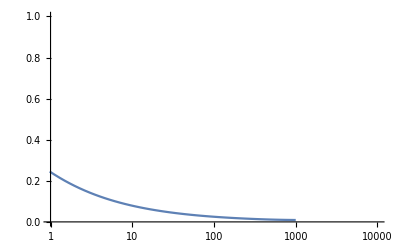

```mathematica
LogLinearPlot[G[1,100,t],{t,0,1000},
PlotRange->{{1,10000}, {0,1}}]
```

### Get an expression for a finite Fourier transform of the incoherent intermediate scattering function. FF are the fourier series elements

```mathematica
ClearAll[d]
F[r_,t_]:=1/(2*Sqrt[d*t*Pi])*Exp[-r^2/(4*d*t)]
Integrate[Exp[-I*k*r]*F[r,t],{r,-Infinity,Infinity},Assumptions-> {Re[1/(d*t)]>0,L∈Reals,L>0,d∈Reals,d>0,t∈Reals}]//FullSimplify

FF[k_,t_]:= 1/L * Integrate[Exp[-I*k*r]*F[r,t],{r,-L,L},Assumptions-> {Re[1/(d*t)]>0,L∈ Reals,L>0}]//FullSimplify
FF[k,t]
```

ⅇ^(-d k^2 t)

(√d ⅇ^(-d k^2 t) √t (Erf[(L-2 ⅈ d k t)/(2 √d √t)]+Erf[(L+2 ⅈ d k t)/(2 √d √t)]))/(2 L √(d t))

### Do the same for the beam profile W(r) to get the Fourier series element W_K

```mathematica
W[r_]:=1/(w*Sqrt[Pi])Exp[-r^2/w^2]

(* Sanity check to make sure this returns the expected W(q)*)
Integrate[Exp[-I*k*r]*W[r],{r,-Infinity,Infinity},Assumptions->{w∈Reals,w>0,L∈Reals,L>0}]

FW[k_]:=1/L*Integrate[Exp[-I*k*r]*W[r],{r,-L,L},Assumptions->{w∈Reals,w>0,L∈Reals,L>0}]
FW[k]
```

ⅇ^(-1/4 k^2 w^2)

(ⅇ^(-1/4 k^2 w^2) (Erf[L/w-(ⅈ k w)/2]+Erf[L/w+(ⅈ k w)/2]))/(2 L)

### Now combine them, to get the spatially-limited autocorrelation G(t;w;L)

```mathematica
BOUND=2
G[t_,w_,L_]:=
Sum[Abs[FW[k]]^2 * FF[k,t],{k,-BOUND,BOUND}]/
Sum[Abs[FW[k]]^2 * FF[k,tp],{k,-BOUND,BOUND}]
```

2

```mathematica
G[t,w,L]
```

$Aborted

```mathematica
G[1,10,100]/.{L->1,d->1,w->1,tp->.0000000000001}
(*Took 143s to evaluate. In the denominator of this, you can see a division by tp, but tp should be zero.*)
```

0.428252+1.21979×10^-17 ⅈ

```mathematica
L=1
d=1
w=1
tp=1*^-10
LogLinearPlot[G[t,10,100],{t,1*^-8,5}]
```

1

1

1

1/10000000000

$Aborted

```mathematica
Erf[I*Infinity]
```

ⅈ ∞

```mathematica
FF[k,t]//PowerExpand
(*The argument to Erf has an L/(2*Sqrt{d*t}) which is problematic at t=0*)
```

(ⅇ^(-d k^2 t) (Erf[(L-2 ⅈ d k t)/(2 √d √t)]+Erf[(L+2 ⅈ d k t)/(2 √d √t)]))/(2 L)